(10 (Sin[3 x]+Sin[2 y]))/(0.5+x^2+y^2)

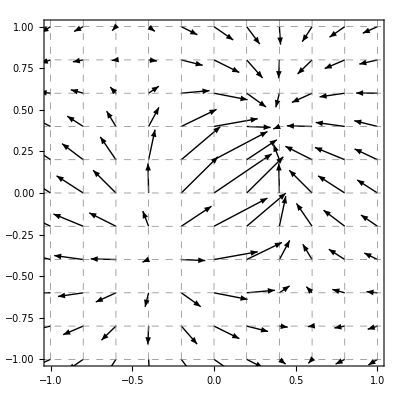

```mathematica
F[x_,y_]=10(Sin[3x]+Sin[2y])/(.5+x^2+y^2)
vecField=VectorPlot[Evaluate[D[F[x,y],{{x,y}}]],{x,-1,1},{y,-1,1},
PlotRange->{{-1,1},{-1,1}},
GridLines->{{-1,-.8,-.6,-.4,-.2,0,.2,.4,.6,.8,1},{-1,-.8,-.6,-.4,-.2,0,.2,.4,.6,.8,1}},
 VectorPoints->11,
VectorStyle-> Black,
VectorScale->{.15,.5},
GridLinesStyle->Directive[Gray,Dashed]]/.Arrow[{p_,q_}]:>Arrow[{p+(q-p)/2,q+(q-p)/2}]
```

```mathematica
Export["~/teaching/mooculus/calculus/vectorFields/egField.png",vecField,ImageResolution->300]
```

~/teaching/mooculus/calculus/vectorFields/egField.png

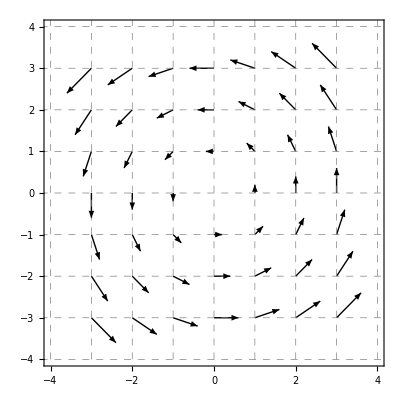

```mathematica
vecField=VectorPlot[{-y,x},{x,-3,3},{y,-3,3},
PlotRange->{{-4,4},{-4,4}},
GridLines->{{-4,-3,-2,-1,0,1,2,3,4},{-4,-3,-2,-1,0,1,2,3,4}},
 VectorPoints->7,
VectorStyle-> Black,
VectorScale->{.1,.6},
GridLinesStyle->Directive[Gray,Dashed]]/.Arrow[{p_,q_}]:>Arrow[{p+(q-p)/2,q+(q-p)/2}]
```

```mathematica
Export["~/teaching/mooculus/calculus/vectorFields/rotField.png",vecField,ImageResolution->300]
```

~/teaching/mooculus/calculus/vectorFields/rotField.png

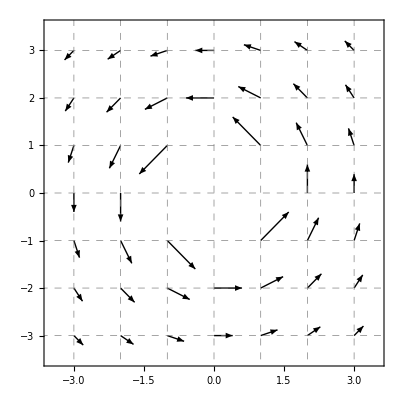

```mathematica
vecField=VectorPlot[Boole[x^2+y^2>1]{-y/(x^2+y^2),x/(x^2+y^2)},{x,-3,3},{y,-3,3},
PlotRange->{{-3.5,3.5},{-3.5,3.5}},
GridLines->{{-4,-3,-2,-1,0,1,2,3,4},{-4,-3,-2,-1,0,1,2,3,4}},
 VectorPoints->7,
VectorStyle-> Black,
VectorScale->{.1,.6},
GridLinesStyle->Directive[Gray,Dashed]]/.Arrow[{p_,q_}]:>Arrow[{p+(q-p)/2,q+(q-p)/2}]
```

```mathematica
Export["~/teaching/mooculus/calculus/vectorFields/rotFieldNot.png",vecField,ImageResolution->300]
```

~/teaching/mooculus/calculus/vectorFields/rotFieldNot.png

```mathematica
vecField=VectorPlot3D[{y,-x,0},{x,-1,1},{y,-1,1},{z,-1,1},VectorStyle-> Black,VectorScale->{.2,.4},VectorPoints->4]
```

-Graphics3D-

```mathematica
Export["~/teaching/mooculus/calculus/vectorFields/rotField3.png",vecField,ImageResolution->300]
```

~/teaching/mooculus/calculus/vectorFields/rotField3.png

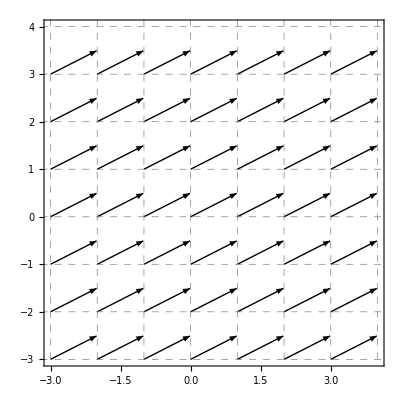

```mathematica
vecField=VectorPlot[{2,1},{x,-3,3},{y,-3,3},
PlotRange->{{-3,4},{-3,4}},
GridLines->{{-4,-3,-2,-1,0,1,2,3,4},{-4,-3,-2,-1,0,1,2,3,4}},
 VectorPoints->7,
VectorStyle-> Black,
VectorScale->{.13,.6},
GridLinesStyle->Directive[Gray,Dashed]]/.Arrow[{p_,q_}]:>Arrow[{p+(q-p)/2,q+(q-p)/2}]
```

```mathematica
Export["~/teaching/mooculus/calculus/vectorFields/constField.png",vecField,ImageResolution->300]
```

~/teaching/mooculus/calculus/vectorFields/constField.png

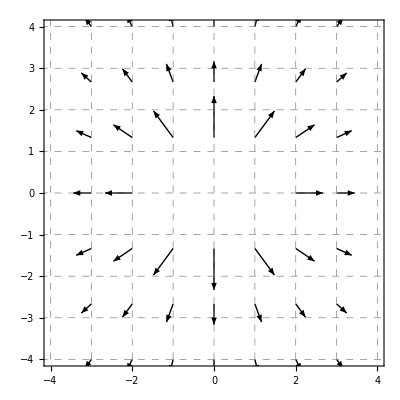

```mathematica
vecField=VectorPlot[Boole[x^2+y^2>1]{x/(x^2+y^2)^(1),y/(x^2+y^2)^(1)},{x,-3,3},{y,-4,4},
PlotRange->{{-4,4},{-4,4}},
GridLines->{{-4,-3,-2,-1,0,1,2,3,4},{-4,-3,-2,-1,0,1,2,3,4}},
 VectorPoints->7,
VectorStyle-> Black,
VectorScale->{.1,.6},
GridLinesStyle->Directive[Gray,Dashed]]/.Arrow[{p_,q_}]:>Arrow[{p+(q-p)/2,q+(q-p)/2}]
```

```mathematica
Export["~/teaching/mooculus/calculus/vectorFields/radField1.png",vecField,ImageResolution->300]
```

~/teaching/mooculus/calculus/vectorFields/radField1.png

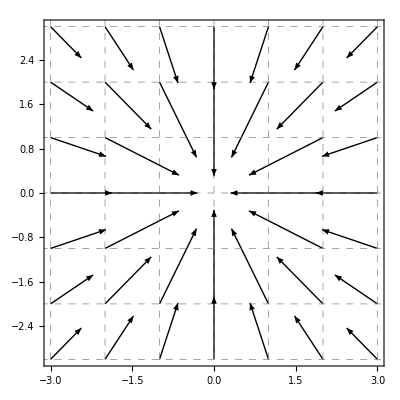

```mathematica
vecField=VectorPlot[Boole[x^2+y^2>3]{-x/(x^2+y^2)^(1),-y/(x^2+y^2)^(1)},{x,-3,3},{y,-3,3},
PlotRange->{{-3,3},{-3,3}},
GridLines->{{-4,-3,-2,-1,0,1,2,3,4},{-4,-3,-2,-1,0,1,2,3,4}},
 VectorPoints->7,
VectorStyle-> Black,
VectorScale->{.2,.3},
GridLinesStyle->Directive[Gray,Dashed]]/.Arrow[{p_,q_}]:>Arrow[{p+(q-p)/2,q+(q-p)/2}]
```

```mathematica
Export["~/teaching/mooculus/calculus/vectorFields/radField2.png",vecField,ImageResolution->300]
```

~/teaching/mooculus/calculus/vectorFields/radField2.png

```mathematica
c
```

-Graphics3D-

```mathematica
vecField=VectorPlot3D[{x,y,z},{x,-1,1},{y,-1,1},{z,-1,1},VectorStyle-> Black,VectorScale->{.4,.2},VectorPoints->5]
```

-Graphics3D-

```mathematica
Export["~/teaching/mooculus/calculus/vectorFields/radField3.png",vecField,ImageResolution->300]
```

~/teaching/mooculus/calculus/vectorFields/radField3.png

```mathematica
/.Arrow[{p_,q_}]:>Arrow[{p+(q-p)/2,q+(q-p)/2}]
```

```mathematica
F[x_,y_]=x^2-y^2;
samples=Flatten[Table[{x,y,0},{x,-1,1,.2},{y,-1,1,.2}],1];
vecField=VectorPlot3D[Evaluate[Append[D[F[x,y],{{x,y}}],0]],{x,-1,1},{y,-1,1},{z,0,.5},VectorPoints->samples,VectorScale->{.1,.6},VectorStyle->Black];
surface=Plot3D[F[x,y],{x,-1,1},{y,-1,1},PlotStyle->Opacity[.5],Mesh->False];
gradSurf=Show[vecField,surface]
```

-Graphics3D-

```mathematica
Export["~/teaching/mooculus/calculus3/vectorFields/gradAndSurf.png",gradSurf,ImageResolution->300]
```

~/teaching/mooculus/calculus3/vectorFields/gradAndSurf.png

-Graphics3D-

-Graphics3D-

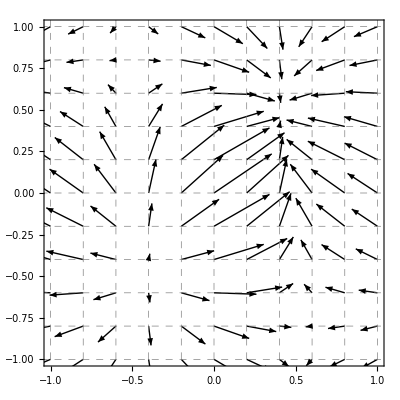

```mathematica
F[x_,y_]=(Sin[3x]+Sin[2y])/(1+x^2+y^2);
samples=Flatten[Table[{x,y,0},{x,-1,1,.2},{y,-1,1,.2}],1];
vecField=VectorPlot3D[Evaluate[Append[D[F[x,y],{{x,y}}],0]],{x,-1,1},{y,-1,1},{z,0,.5},VectorPoints->samples,VectorScale->{.1,.4},VectorStyle->Black];
surface=Plot3D[F[x,y],{x,-1,1},{y,-1,1},PlotStyle->Opacity[.5],Mesh->False,PlotRange->{-2,2},BoxRatios->{1,1,1}]
gradSurf=Show[vecField,surface,PlotRange->{-2,2}]

vecField=VectorPlot[Evaluate[D[F[x,y],{{x,y}}]],{x,-1,1},{y,-1,1},
PlotRange->{{-1,1},{-1,1}},
GridLines->{{-1,-.8,-.6,-.4,-.2,0,.2,.4,.6,.8,1},{-1,-.8,-.6,-.4,-.2,0,.2,.4,.6,.8,1}},
 VectorPoints->11,
VectorStyle-> Black,
VectorScale->{.15,.5},
GridLinesStyle->Directive[Gray,Dashed]]/.Arrow[{p_,q_}]:>Arrow[{p+(q-p)/2,q+(q-p)/2}]
```

```mathematica
Export["~/teaching/mooculus/calculus/vectorFields/surf1.png",surface,ImageResolution->300]
```

~/teaching/mooculus/calculus/vectorFields/surf1.png

```mathematica
Export["~/teaching/mooculus/calculus/vectorFields/gradField1.png",vecField,ImageResolution->300]
```

~/teaching/mooculus/calculus/vectorFields/gradField1.png

```mathematica
Export["~/teaching/mooculus/calculus/vectorFields/gradSurf1.png",gradSurf,ImageResolution->300]
```

~/teaching/mooculus/calculus/vectorFields/gradSurf1.png

```mathematica
"~/teaching/mooculus/calculus/vectorFields/gradSurf1.png"
```

1/(√(x^2+y^2))

-Graphics3D-

-Graphics3D-

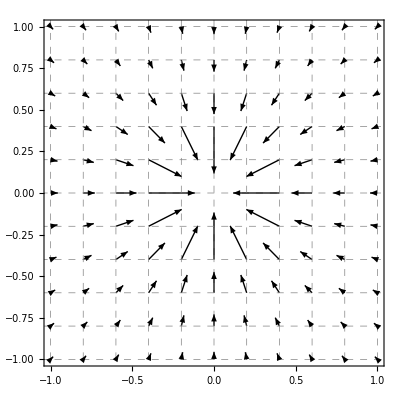

```mathematica
F[x_,y_]=1/Sqrt[x^2+y^2]
samples=Flatten[Table[{x,y,0},{x,-1,1,.2},{y,-1,1,.2}],1];
vecField=VectorPlot3D[Evaluate[Append[D[F[x,y],{{x,y}}],0]],{x,-1,1},{y,-1,1},{z,0,.5},VectorPoints->samples,VectorScale->{.1,.4},VectorStyle->Black];
surface=Plot3D[F[x,y],{x,-1,1},{y,-1,1},PlotStyle->Opacity[.5],Mesh->False,PlotRange->{0,10},BoxRatios->{1,1,1}]
gradSurf=Show[vecField,surface,PlotRange->{0,10}]

vecField=VectorPlot[Boole[x^2+y^2>.1]{-x/Sqrt[(x^2+y^2)]^3,-y/Sqrt[(x^2+y^2)]^3},{x,-1,1},{y,-1,1},
PlotRange->{{-1,1},{-1,1}},
GridLines->{{-1,-.8,-.6,-.4,-.2,0,.2,.4,.6,.8,1},{-1,-.8,-.6,-.4,-.2,0,.2,.4,.6,.8,1}},
 VectorPoints->11,
VectorStyle-> Black,
VectorScale->{.1,.9},
GridLinesStyle->Directive[Gray,Dashed]]/.Arrow[{p_,q_}]:>Arrow[{p+(q-p)/2,q+(q-p)/2}]
```

```mathematica
Export["~/teaching/mooculus/calculus/vectorFields/surf2.png",surface,ImageResolution->300]
```

~/teaching/mooculus/calculus/vectorFields/surf2.png

```mathematica
Export["~/teaching/mooculus/calculus/vectorFields/gradField2.png",vecField,ImageResolution->300]
```

~/teaching/mooculus/calculus/vectorFields/gradField2.png

```mathematica
Export["~/teaching/mooculus/calculus/vectorFields/gradSurf2.png",gradSurf,ImageResolution->300]
```

~/teaching/mooculus/calculus/vectorFields/gradSurf2.png

```mathematica
1
```

1

```mathematica
F[x_,y_]=x^2-y^2
samples=Flatten[Table[{x,y,0},{x,-1,1,.2},{y,-1,1,.2}],1];
vecField=VectorPlot3D[Evaluate[Append[D[F[x,y],{{x,y}}],0]],{x,-1,1},{y,-1,1},{z,0,.5},VectorPoints->samples,VectorScale->{.1,.6},VectorStyle->Black];
surface=Plot3D[F[x,y],{x,-1,1},{y,-1,1},PlotStyle->Opacity[.5],Mesh->False];
gradSurf=Show[vecField,surface]
```

x^2-y^2

-Graphics3D-

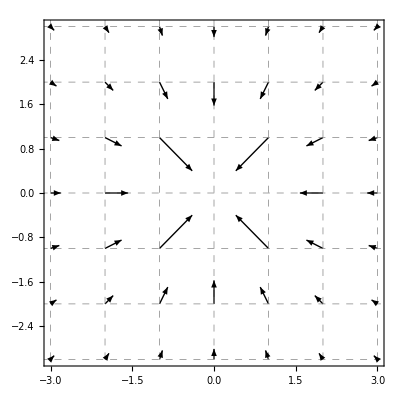

```mathematica
vecField=VectorPlot[Boole[x^2+y^2>1]{-x/(x^2+y^2)^(3/2),-y/(x^2+y^2)^(3/2)},{x,-3,3},{y,-3,3},
PlotRange->{{-3,3},{-3,3}},
GridLines->{{-4,-3,-2,-1,0,1,2,3,4},{-4,-3,-2,-1,0,1,2,3,4}},
 VectorPoints->7,
VectorStyle-> Black,
VectorScale->{.1,.5},
GridLinesStyle->Directive[Gray,Dashed]]/.Arrow[{p_,q_}]:>Arrow[{p+(q-p)/2,q+(q-p)/2}]
```

```mathematica
Export["~/teaching/mooculus/calculus3/vectorFields/radField4.png",vecField]
```

~/teaching/mooculus/calculus3/vectorFields/radField4.png

```mathematica
Integrate[-y/(x^2+y^2),x]
Integrate[x/(x^2+y^2),y]
```

-ArcTan[x/y]

ArcTan[y/x]

```mathematica
Simplify[(2 x^2)/((x^2+y^2)^2)+(2 y^2)/((x^2+y^2)^2)-2/(x^2+y^2)]
```

0

```mathematica
surface=Plot3D[ArcTan[y,x],{x,-1,1},{y,-1,1},PlotStyle->Opacity[.5],Mesh->False,PlotRange->{-6,6}]
```

-Graphics3D-